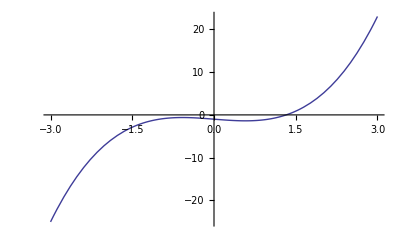

6 x

derF= -1+3 x^2

-(1+1/x^2)/(2 (-1/x+x)^(3/2))

q = 5/(6 √6)

q < 1 - True

m/(1  -  q) (3/2-√(6/5))/(1-5/(6 √6))

delta - 1/2

m/(1  -  q) <= delta - False

$Aborted

x1 = -10.001

```mathematica
Clear[x];
f=x^3 -x -1;
Plot[f,{x,-3,3}]
derF = D[f,x];
Print[D[derF,x]];
Print["derF= ",derF];
ϕ = 1/(√(x -1/x));
checkTheorem[f_,segm_]:=(
Clear[x];
delta = Abs[segm[[2]]-segm[[1]]]/2;
x0=segm[[2]]-delta;
derF1=D[f,x];
Plot[derF1,{x,-3,3}]
Print[derF1];
q=Abs[-(1+1/segm[[2]]^2)/(2 (-1/segm[[2]]+segm[[2]])^(3/2))];
x=x0;
Print["q = ",q ];
Print["q < 1 - ",q < 1];
m = Abs[x0 - f];
Print["m/(1  -  q) ",m/(1 - q) ];
Print["delta - ", delta];

Print["m/(1  -  q) <= delta - ",m/(1 - q) <= delta];

Return[x0];
);

defineRoot[f_, start_, end_] := (
Clear[x];
x00 = checkTheorem[f,{start,end}];
xn = x00;
While[Abs[xn - x00] > 0.5 * 10^(-3)  || xn == x00, 
	Clear[x];
         x00 = xn;
          x = x00;
	xn = ϕ;         
];
Return[xn];
);
x1 = defineRoot[ϕ,1, 2];
Print["x1 = ", N[x1]];
Clear[x];
```